# Rigid bodies, plastic impact

-Graphics-

## Kinematics

We start with a simple manipulator, moving base (that mimics the spacecraft position and orientation) and two rotational links.

```mathematica
Mrotztrasl[α_,point_]:={{Cos[α],-Sin[α],0,point[[1]]},{Sin[α],Cos[α],0,point[[2]]},{0,0,1,point[[3]]},{0,0,0,1}};
Mrotztrasl[α,{p1,p2,p3}]//MatrixForm
```

(Cos[α] | -Sin[α] | 0 | p1
Sin[α] | Cos[α] | 0 | p2
0 | 0 | 1 | p3
0 | 0 | 0 | 1)

```mathematica
M01=Mrotztrasl[θ1[t],{x[t],y[t],0}];M01//MatrixForm
```

(Cos[θ1[t]] | -Sin[θ1[t]] | 0 | x[t]
Sin[θ1[t]] | Cos[θ1[t]] | 0 | y[t]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
M12=Mrotztrasl[θ2[t],{l1 Cos[θ2[t]],l1 Sin[θ2[t]],0}];M12//MatrixForm
```

(Cos[θ2[t]] | -Sin[θ2[t]] | 0 | l1 Cos[θ2[t]]
Sin[θ2[t]] | Cos[θ2[t]] | 0 | l1 Sin[θ2[t]]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
M23=Mrotztrasl[θ3[t],{l2 Cos[θ3[t]],l2 Sin[θ3[t]],0}];M23//MatrixForm
```

(Cos[θ3[t]] | -Sin[θ3[t]] | 0 | l2 Cos[θ3[t]]
Sin[θ3[t]] | Cos[θ3[t]] | 0 | l2 Sin[θ3[t]]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
M02=M01.M12;
```

```mathematica
M03=M02.M23;
```

### Origin points

```mathematica
origin={0,0,0,1};
```

```mathematica
O1=M01.origin;O1//MatrixForm
```

(x[t]
y[t]
0
1)

```mathematica
O2=M02.origin;O2//MatrixForm
```

(l1 Cos[θ1[t]] Cos[θ2[t]]-l1 Sin[θ1[t]] Sin[θ2[t]]+x[t]
l1 Cos[θ2[t]] Sin[θ1[t]]+l1 Cos[θ1[t]] Sin[θ2[t]]+y[t]
0
1)

```mathematica
O3=M03.origin;O3//MatrixForm
```

(l1 Cos[θ1[t]] Cos[θ2[t]]-l1 Sin[θ1[t]] Sin[θ2[t]]+l2 Cos[θ3[t]] (Cos[θ1[t]] Cos[θ2[t]]-Sin[θ1[t]] Sin[θ2[t]])+l2 (-Cos[θ2[t]] Sin[θ1[t]]-Cos[θ1[t]] Sin[θ2[t]]) Sin[θ3[t]]+x[t]
l1 Cos[θ2[t]] Sin[θ1[t]]+l1 Cos[θ1[t]] Sin[θ2[t]]+l2 Cos[θ3[t]] (Cos[θ2[t]] Sin[θ1[t]]+Cos[θ1[t]] Sin[θ2[t]])+l2 (Cos[θ1[t]] Cos[θ2[t]]-Sin[θ1[t]] Sin[θ2[t]]) Sin[θ3[t]]+y[t]
0
1)

Jacobian matrix:

```mathematica
J=Simplify[D[O3[[1;;2]],{{x[t],y[t],θ1[t],θ2[t],θ3[t]}}]];J//MatrixForm
```

(1 | 0 | -l1 Sin[θ1[t]+θ2[t]]-l2 Sin[θ1[t]+θ2[t]+θ3[t]] | -l1 Sin[θ1[t]+θ2[t]]-l2 Sin[θ1[t]+θ2[t]+θ3[t]] | -l2 Sin[θ1[t]+θ2[t]+θ3[t]]
0 | 1 | l1 Cos[θ1[t]+θ2[t]]+l2 Cos[θ1[t]+θ2[t]+θ3[t]] | l1 Cos[θ1[t]+θ2[t]]+l2 Cos[θ1[t]+θ2[t]+θ3[t]] | l2 Cos[θ1[t]+θ2[t]+θ3[t]])

```mathematica
J. D[{x[t],y[t],θ1[t],θ2[t],θ3[t]},t]==D[O3[[1;;2]],t]//Simplify
```

True

### Plot a 2D scheme of the robot

```mathematica
param={l1->2.0,l2->3.0,θ1[t]->0.2,θ2[t]->π/6,θ3[t]->π/6,x[t]->1,y[t]->2,m1->5,m2->6,mb->10,m->30,r->0.5};
paraml={l1->2.0,l2->3.0};
```

```mathematica
RobotPlot=ListLinePlot[{O1[[1;;2]]/.param,O2[[1;;2]]/.param,O3[[1;;2]]/.param},PlotRange->{{0,7},{0,7}},PlotMarkers->{Automatic, 5}];
```

```mathematica
labels={"X0","Y0"};
```

```mathematica
For[i=1,i<3,i++,u={0,0};(*initializing u as a null 3 elements vector*)u⟦i⟧=1;(*Setting the i-th element of u equal to 1,to have a unit vector*)RF0arrow[i]=Graphics[{Thickness[0.010],Red,Arrowheads[0.04],
Text[labels⟦i⟧,2 u+0.07],Arrow[{{0,0},2 u}]},Axes->True]];
```

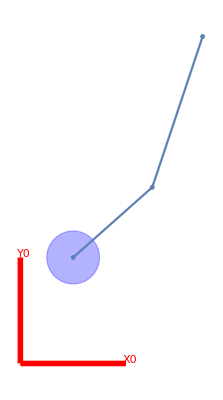

```mathematica
Show[{Block[{r=0.5},Graphics[{Blue,EdgeForm[Thick],Opacity[0.3],Disk[O1[[1;;2]]/.param,r]}]],RobotPlot,RF0arrow[1],RF0arrow[2]}]
```

```mathematica
Manipulate[Show[{ListLinePlot[{O1[[1;;2]]/.{x[t]->a1,y[t]->a2,θ1[t]->a3,θ2[t]->a4,θ3[t]->a5},O2[[1;;2]]/.{x[t]->a1,y[t]->a2,θ1[t]->a3,θ2[t]->a4,θ3[t]->a5},O3[[1;;2]]/.{x[t]->a1,y[t]->a2,θ1[t]->a3,θ2[t]->a4,θ3[t]->a5}}/.paraml,PlotRange->{{0,8},{0,8}},AspectRatio->1,PlotMarkers->{Automatic, 5}]},Block[{r=0.5},Graphics[{EdgeForm[Thick],Blue,Opacity[0.3],Disk[{a1,a2},r],Thickness[0.007],Opacity[0.5],Red,Arrowheads[0.04],Arrow[{{a1,a2},{a1+l1 Cos[a3]/.param,a2+l1 Sin[a3]/.param}}],Arrow[{{a1,a2},{a1-l1 Sin[a3]/.param,a2+l1 Cos[a3]/.param}}]}]],RF0arrow[1],RF0arrow[2]],{a1,0,3},{a2,0,3},{a3,0,π/4},{a4,0,π/4},{a5,0,π/4}]
```

## Dynamics

## Manipulator

### IR method

The mass is considered lumped, hence the pseudo inertia tensor can be written like this:

```mathematica
Ixx2=1/4m1 l1^2;
Ixx3=1/4 m2 l2^2;
```

Inertia frame in the com of the round base:

```mathematica
J11={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,mb}};J11//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | mb)

```mathematica
J10=Simplify[M01.J11.Transpose[M01]];J10//MatrixForm
```

(mb x[t]^2 | mb x[t] y[t] | 0 | mb x[t]
mb x[t] y[t] | mb y[t]^2 | 0 | mb y[t]
0 | 0 | 0 | 0
mb x[t] | mb y[t] | 0 | mb)

```mathematica
J22={{Ixx2,0,0,-l1/2 m1},{0,0,0,0},{0,0,0,0},{-l1/2 m1,0,0,m1}};J22//MatrixForm
```

((l1^2 m1)/4 | 0 | 0 | -(l1 m1)/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(l1 m1)/2 | 0 | 0 | m1)

```mathematica
J20=Simplify[M02.J22.Transpose[M02]];
```

```mathematica
J33={{Ixx3,0,0,-l2/2 m2},{0,0,0,0},{0,0,0,0},{-l2/2 m2,0,0,m2}};J33//MatrixForm
```

((l2^2 m2)/4 | 0 | 0 | -(l2 m2)/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(l2 m2)/2 | 0 | 0 | m2)

```mathematica
J30=Simplify[M03.J33.Transpose[M03]];
```

```mathematica
W01=Simplify[D[M01,t].Inverse[M01]];W01//MatrixForm
```

(0 | -θ1'[t] | 0 | x'[t]+y[t] θ1'[t]
θ1'[t] | 0 | 0 | y'[t]-x[t] θ1'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
W02=Simplify[D[M02,t].Inverse[M02]];W02//MatrixForm
```

(0 | -θ1'[t]-θ2'[t] | 0 | x'[t]+y[t] (θ1'[t]+θ2'[t])
θ1'[t]+θ2'[t] | 0 | 0 | y'[t]-x[t] (θ1'[t]+θ2'[t])
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
W03=Simplify[D[M03,t].Inverse[M03]];W03//MatrixForm
```

(0 | -θ1'[t]-θ2'[t]-θ3'[t] | 0 | x'[t]+l1 Sin[θ1[t]+θ2[t]] θ3'[t]+y[t] (θ1'[t]+θ2'[t]+θ3'[t])
θ1'[t]+θ2'[t]+θ3'[t] | 0 | 0 | y'[t]-l1 Cos[θ1[t]+θ2[t]] θ3'[t]-x[t] (θ1'[t]+θ2'[t]+θ3'[t])
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
T1=Simplify[1/2Tr[W01.J10.Transpose[W01]]];
T2=Simplify[1/2Tr[W02.J20.Transpose[W02]]];
T3=Simplify[1/2Tr[W03.J30.Transpose[W03]]];
```

The potential energy of body i, denoted by Ui, consists of two parts; one due to the gravity gradient and the other due to the elastic strain energy stored in the flexible body. The effect of the former is much smaller than the latter and is neglected here. Hence the potential energy of a rigid body is equal to zero.

```mathematica
L=T1+T2+T3;
```

```mathematica
eq1=Simplify[D[D[L,x'[t]],t]-D[L,x[t]]==Fx];
eq2=Simplify[D[D[L,y'[t]],t]-D[L,y[t]]==Fy];
eq3=Simplify[D[D[L,θ1'[t]],t]-D[L,θ1[t]]==τ1];
eq4=Simplify[D[D[L,θ2'[t]],t]-D[L,θ2[t]]==τ2];
eq5=Simplify[D[D[L,θ3'[t]],t]-D[L,θ3[t]]==τ3];
```

```mathematica
sol=Solve[{eq1,eq2,eq3,eq4,eq5},{Fx,Fy,τ1,τ2,τ3}][[1]];
```

```mathematica
Eq1=sol[[1,2]];
Eq2=sol[[2,2]];
Eq3=sol[[3,2]];
Eq4=sol[[4,2]];
Eq5=sol[[5,2]];
```

```mathematica
{c,M}=Normal@CoefficientArrays[{Eq1,Eq2,Eq3,Eq4,Eq5},{x''[t],y''[t],θ1''[t],θ2''[t],θ3''[t]}];
```

```mathematica
MatrixForm[M]
```

(m1+m2+mb | 0 | -1/2 l1 m1 Sin[θ1[t]+θ2[t]]-l1 m2 Sin[θ1[t]+θ2[t]]-1/2 l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]] | -1/2 l1 m1 Sin[θ1[t]+θ2[t]]-l1 m2 Sin[θ1[t]+θ2[t]]-1/2 l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]] | -1/2 l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]]
0 | m1+m2+mb | 1/2 l1 m1 Cos[θ1[t]+θ2[t]]+l1 m2 Cos[θ1[t]+θ2[t]]+1/2 l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]] | 1/2 l1 m1 Cos[θ1[t]+θ2[t]]+l1 m2 Cos[θ1[t]+θ2[t]]+1/2 l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]] | 1/2 l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]]
-1/2 l1 m1 Sin[θ1[t]+θ2[t]]-l1 m2 Sin[θ1[t]+θ2[t]]-1/2 l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]] | 1/2 l1 m1 Cos[θ1[t]+θ2[t]]+l1 m2 Cos[θ1[t]+θ2[t]]+1/2 l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]] | (l1^2 m1)/4+l1^2 m2+(l2^2 m2)/4+l1 l2 m2 Cos[θ3[t]] | (l1^2 m1)/4+l1^2 m2+(l2^2 m2)/4+l1 l2 m2 Cos[θ3[t]] | (l2^2 m2)/4+1/2 l1 l2 m2 Cos[θ3[t]]
-1/2 l1 m1 Sin[θ1[t]+θ2[t]]-l1 m2 Sin[θ1[t]+θ2[t]]-1/2 l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]] | 1/2 l1 m1 Cos[θ1[t]+θ2[t]]+l1 m2 Cos[θ1[t]+θ2[t]]+1/2 l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]] | (l1^2 m1)/4+l1^2 m2+(l2^2 m2)/4+l1 l2 m2 Cos[θ3[t]] | (l1^2 m1)/4+l1^2 m2+(l2^2 m2)/4+l1 l2 m2 Cos[θ3[t]] | (l2^2 m2)/4+1/2 l1 l2 m2 Cos[θ3[t]]
-1/2 l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]] | 1/2 l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]] | (l2^2 m2)/4+1/2 l1 l2 m2 Cos[θ3[t]] | (l2^2 m2)/4+1/2 l1 l2 m2 Cos[θ3[t]] | (l2^2 m2)/4)

```mathematica
MatrixForm[c]
```

(-1/2 l1 m1 Cos[θ1[t]+θ2[t]] θ1'[t]^2-l1 m2 Cos[θ1[t]+θ2[t]] θ1'[t]^2-1/2 l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]] θ1'[t]^2-l1 m1 Cos[θ1[t]+θ2[t]] θ1'[t] θ2'[t]-2 l1 m2 Cos[θ1[t]+θ2[t]] θ1'[t] θ2'[t]-l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]] θ1'[t] θ2'[t]-1/2 l1 m1 Cos[θ1[t]+θ2[t]] θ2'[t]^2-l1 m2 Cos[θ1[t]+θ2[t]] θ2'[t]^2-1/2 l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]] θ2'[t]^2-l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]] θ1'[t] θ3'[t]-l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]] θ2'[t] θ3'[t]-1/2 l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]] θ3'[t]^2
-1/2 l1 m1 Sin[θ1[t]+θ2[t]] θ1'[t]^2-l1 m2 Sin[θ1[t]+θ2[t]] θ1'[t]^2-1/2 l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]] θ1'[t]^2-l1 m1 Sin[θ1[t]+θ2[t]] θ1'[t] θ2'[t]-2 l1 m2 Sin[θ1[t]+θ2[t]] θ1'[t] θ2'[t]-l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]] θ1'[t] θ2'[t]-1/2 l1 m1 Sin[θ1[t]+θ2[t]] θ2'[t]^2-l1 m2 Sin[θ1[t]+θ2[t]] θ2'[t]^2-1/2 l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]] θ2'[t]^2-l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]] θ1'[t] θ3'[t]-l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]] θ2'[t] θ3'[t]-1/2 l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]] θ3'[t]^2
-l1 l2 m2 Sin[θ3[t]] θ1'[t] θ3'[t]-l1 l2 m2 Sin[θ3[t]] θ2'[t] θ3'[t]-1/2 l1 l2 m2 Sin[θ3[t]] θ3'[t]^2
-l1 l2 m2 Sin[θ3[t]] θ1'[t] θ3'[t]-l1 l2 m2 Sin[θ3[t]] θ2'[t] θ3'[t]-1/2 l1 l2 m2 Sin[θ3[t]] θ3'[t]^2
1/2 l1 l2 m2 Sin[θ3[t]] θ1'[t]^2+l1 l2 m2 Sin[θ3[t]] θ1'[t] θ2'[t]+1/2 l1 l2 m2 Sin[θ3[t]] θ2'[t]^2)

Equation of motion: Mp^(..)+ c = u

### Classic Lagrangian method

```mathematica
COM1=(M01.{0,0,0,1})[[1;;2]];
COM2=(M02.{-l1/2,0,0,1})[[1;;2]];
COM3=(M03.{-l2/2,0,0,1})[[1;;2]];
```

```mathematica
v1=D[COM1,t];
v2=D[COM2,t];
v3=D[COM3,t];
```

```mathematica
v1square=Simplify[v1[[1]]^2+v1[[2]]^2];
v2square=Simplify[v2[[1]]^2+v2[[2]]^2];
v3square=Simplify[v3[[1]]^2+v3[[2]]^2];
```

CoM inertia:

```mathematica
Iz2=m1 (l1/2)^2;
Iz3=m2(l2/2)^2;
```

```mathematica
k1mid=1/2mb v1square;
k2mid=1/2 m1 v2square+1/2 Iz2(θ1'[t]+θ2'[t])^2;
k3mid=1/2m2 v3square+1/2 Iz3(θ1'[t]+θ2'[t]+θ3'[t])^2;
```

```mathematica
lmid=k1mid+k2mid+k3mid;
```

```mathematica
eq1Mid=Simplify[D[D[lmid,x'[t]],t]-D[lmid,x[t]]-Fx==0];
eq2Mid=Simplify[D[D[lmid,y'[t]],t]-D[lmid,y[t]]-Fy==0];
eq3Mid=Simplify[D[D[lmid,θ1'[t]],t]-D[lmid,θ1[t]]-τ1==0];
eq4Mid=Simplify[D[D[lmid,θ2'[t]],t]-D[lmid,θ2[t]]-τ2==0];
eq5Mid=Simplify[D[D[lmid,θ3'[t]],t]-D[lmid,θ3[t]]-τ3==0];
```

```mathematica
sol2=Solve[{eq1Mid,eq2Mid,eq3Mid,eq4Mid,eq5Mid},{Fx,Fy,τ1,τ2,τ3}][[1]];
Eq1Mid=sol2[[1,2]];
Eq2Mid=sol2[[2,2]];
Eq3Mid=sol2[[3,2]];
Eq4Mid=sol2[[4,2]];
Eq5Mid=sol2[[5,2]];
```

```mathematica
{c2,M2}=Normal@CoefficientArrays[{Eq1Mid,Eq2Mid,Eq3Mid,Eq4Mid,Eq5Mid},{x''[t],y''[t],θ1''[t],θ2''[t],θ3''[t]}];
```

```mathematica
MatrixForm[M2]
```

(m1+m2+mb | 0 | -1/2 l1 m1 Sin[θ1[t]+θ2[t]]-l1 m2 Sin[θ1[t]+θ2[t]]-1/2 l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]] | -1/2 l1 m1 Sin[θ1[t]+θ2[t]]-l1 m2 Sin[θ1[t]+θ2[t]]-1/2 l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]] | -1/2 l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]]
0 | m1+m2+mb | 1/2 l1 m1 Cos[θ1[t]+θ2[t]]+l1 m2 Cos[θ1[t]+θ2[t]]+1/2 l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]] | 1/2 l1 m1 Cos[θ1[t]+θ2[t]]+l1 m2 Cos[θ1[t]+θ2[t]]+1/2 l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]] | 1/2 l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]]
-1/2 l1 m1 Sin[θ1[t]+θ2[t]]-l1 m2 Sin[θ1[t]+θ2[t]]-1/2 l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]] | 1/2 l1 m1 Cos[θ1[t]+θ2[t]]+l1 m2 Cos[θ1[t]+θ2[t]]+1/2 l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]] | (l1^2 m1)/2+l1^2 m2+(l2^2 m2)/2+l1 l2 m2 Cos[θ3[t]] | (l1^2 m1)/2+l1^2 m2+(l2^2 m2)/2+l1 l2 m2 Cos[θ3[t]] | (l2^2 m2)/2+1/2 l1 l2 m2 Cos[θ3[t]]
-1/2 l1 m1 Sin[θ1[t]+θ2[t]]-l1 m2 Sin[θ1[t]+θ2[t]]-1/2 l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]] | 1/2 l1 m1 Cos[θ1[t]+θ2[t]]+l1 m2 Cos[θ1[t]+θ2[t]]+1/2 l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]] | (l1^2 m1)/2+l1^2 m2+(l2^2 m2)/2+l1 l2 m2 Cos[θ3[t]] | (l1^2 m1)/2+l1^2 m2+(l2^2 m2)/2+l1 l2 m2 Cos[θ3[t]] | (l2^2 m2)/2+1/2 l1 l2 m2 Cos[θ3[t]]
-1/2 l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]] | 1/2 l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]] | (l2^2 m2)/2+1/2 l1 l2 m2 Cos[θ3[t]] | (l2^2 m2)/2+1/2 l1 l2 m2 Cos[θ3[t]] | (l2^2 m2)/2)

```mathematica
MatrixForm[c2]
```

(-1/2 l1 m1 Cos[θ1[t]+θ2[t]] θ1'[t]^2-l1 m2 Cos[θ1[t]+θ2[t]] θ1'[t]^2-1/2 l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]] θ1'[t]^2-l1 m1 Cos[θ1[t]+θ2[t]] θ1'[t] θ2'[t]-2 l1 m2 Cos[θ1[t]+θ2[t]] θ1'[t] θ2'[t]-l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]] θ1'[t] θ2'[t]-1/2 l1 m1 Cos[θ1[t]+θ2[t]] θ2'[t]^2-l1 m2 Cos[θ1[t]+θ2[t]] θ2'[t]^2-1/2 l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]] θ2'[t]^2-l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]] θ1'[t] θ3'[t]-l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]] θ2'[t] θ3'[t]-1/2 l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]] θ3'[t]^2
-1/2 l1 m1 Sin[θ1[t]+θ2[t]] θ1'[t]^2-l1 m2 Sin[θ1[t]+θ2[t]] θ1'[t]^2-1/2 l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]] θ1'[t]^2-l1 m1 Sin[θ1[t]+θ2[t]] θ1'[t] θ2'[t]-2 l1 m2 Sin[θ1[t]+θ2[t]] θ1'[t] θ2'[t]-l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]] θ1'[t] θ2'[t]-1/2 l1 m1 Sin[θ1[t]+θ2[t]] θ2'[t]^2-l1 m2 Sin[θ1[t]+θ2[t]] θ2'[t]^2-1/2 l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]] θ2'[t]^2-l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]] θ1'[t] θ3'[t]-l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]] θ2'[t] θ3'[t]-1/2 l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]] θ3'[t]^2
-l1 l2 m2 Sin[θ3[t]] θ1'[t] θ3'[t]-l1 l2 m2 Sin[θ3[t]] θ2'[t] θ3'[t]-1/2 l1 l2 m2 Sin[θ3[t]] θ3'[t]^2
-l1 l2 m2 Sin[θ3[t]] θ1'[t] θ3'[t]-l1 l2 m2 Sin[θ3[t]] θ2'[t] θ3'[t]-1/2 l1 l2 m2 Sin[θ3[t]] θ3'[t]^2
1/2 l1 l2 m2 Sin[θ3[t]] θ1'[t]^2+l1 l2 m2 Sin[θ3[t]] θ1'[t] θ2'[t]+1/2 l1 l2 m2 Sin[θ3[t]] θ2'[t]^2)

```mathematica
c2==c
```

True

```mathematica
M[[1]]==M2[[1]]
M[[2]]==M2[[2]]
FullSimplify[M[[3]]==M2[[3]]]
FullSimplify[M[[4]]==M2[[4]]]
FullSimplify[M[[5]]==M2[[5]]]
```

True

True

{0,0,-(l1^2 m1)/4-(l2^2 m2)/4,-(l1^2 m1)/4-(l2^2 m2)/4,-(l2^2 m2)/4}=={0,0,0,0,0}

{0,0,-(l1^2 m1)/4-(l2^2 m2)/4,-(l1^2 m1)/4-(l2^2 m2)/4,-(l2^2 m2)/4}=={0,0,0,0,0}

{0,0,-(l2^2 m2)/4,-(l2^2 m2)/4,-(l2^2 m2)/4}=={0,0,0,0,0}

```mathematica
Inverse[M]
```

Inverse[{{m1+m2+mb,0,-1/2 l1 m1 Sin[θ1[t]+θ2[t]]-l1 m2 Sin[θ1[t]+θ2[t]]-1/2 l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]],-1/2 l1 m1 Sin[θ1[t]+θ2[t]]-l1 m2 Sin[θ1[t]+θ2[t]]-1/2 l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]],-1/2 l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]]},{0,m1+m2+mb,1/2 l1 m1 Cos[θ1[t]+θ2[t]]+l1 m2 Cos[θ1[t]+θ2[t]]+1/2 l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]],1/2 l1 m1 Cos[θ1[t]+θ2[t]]+l1 m2 Cos[θ1[t]+θ2[t]]+1/2 l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]],1/2 l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]]},{-1/2 l1 m1 Sin[θ1[t]+θ2[t]]-l1 m2 Sin[θ1[t]+θ2[t]]-1/2 l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]],1/2 l1 m1 Cos[θ1[t]+θ2[t]]+l1 m2 Cos[θ1[t]+θ2[t]]+1/2 l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]],(l1^2 m1)/4+l1^2 m2+(l2^2 m2)/4+l1 l2 m2 Cos[θ3[t]],(l1^2 m1)/4+l1^2 m2+(l2^2 m2)/4+l1 l2 m2 Cos[θ3[t]],(l2^2 m2)/4+1/2 l1 l2 m2 Cos[θ3[t]]},{-1/2 l1 m1 Sin[θ1[t]+θ2[t]]-l1 m2 Sin[θ1[t]+θ2[t]]-1/2 l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]],1/2 l1 m1 Cos[θ1[t]+θ2[t]]+l1 m2 Cos[θ1[t]+θ2[t]]+1/2 l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]],(l1^2 m1)/4+l1^2 m2+(l2^2 m2)/4+l1 l2 m2 Cos[θ3[t]],(l1^2 m1)/4+l1^2 m2+(l2^2 m2)/4+l1 l2 m2 Cos[θ3[t]],(l2^2 m2)/4+1/2 l1 l2 m2 Cos[θ3[t]]},{-1/2 l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]],1/2 l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]],(l2^2 m2)/4+1/2 l1 l2 m2 Cos[θ3[t]],(l2^2 m2)/4+1/2 l1 l2 m2 Cos[θ3[t]],(l2^2 m2)/4}}]

## Satellite

-Graphics-

Let’s consider a circula spinning satellite. In 2D, we have 3 DoF: x, y, and rotation around z.
Coordinats refered to the COM:

```mathematica
ψ={X[t],Y[t],Ω[t]};
ψ'=D[ψ,t];
```

The jacobian describe the relationship between the velocity of the dof and the contact point:

```mathematica
Ms01=Mrotztrasl[Ω[t],{r Cos[θ],r Sin[θ],0}];Ms01//MatrixForm
```

(Cos[Ω[t]] | -Sin[Ω[t]] | 0 | r Cos[θ]
Sin[Ω[t]] | Cos[Ω[t]] | 0 | r Sin[θ]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
contactPlocal=Ms01.origin
contactP=Simplify[{X[t],Y[t]}+Ms01[[1;;2,1;;2]].contactPlocal[[1;;2]]];contactP//MatrixForm
velContactP=D[contactP,t];velContactP//MatrixForm
```

{r Cos[θ],r Sin[θ],0,1}

(r Cos[θ+Ω[t]]+X[t]
r Sin[θ+Ω[t]]+Y[t])

(X'[t]-r Sin[θ+Ω[t]] Ω'[t]
Y'[t]+r Cos[θ+Ω[t]] Ω'[t])

```mathematica
Js=D[contactP,{{X[t],Y[t],Ω[t]}}];Js//MatrixForm
```

(1 | 0 | -r Sin[θ+Ω[t]]
0 | 1 | r Cos[θ+Ω[t]])

```mathematica
Transpose[Js]//MatrixForm
```

(1 | 0
0 | 1
-r Sin[θ+Ω[t]] | r Cos[θ+Ω[t]])

```mathematica
Js.ψ'==velContactP//Simplify
```

True

```mathematica
Iz=1/2m r^2;
```

```mathematica
T=1/2 m(ψ'[[1]]^2+ψ'[[2]]^2)+1/2Iz ψ'[[3]]^2
```

1/2 m (X'[t]^2+Y'[t]^2)+1/4 m r^2 Ω'[t]^2

```mathematica
eq1S=Simplify[D[D[T,X'[t]],t]-D[T,X[t]]-fx==0];
eq2S=Simplify[D[D[T,Y'[t]],t]-D[T,Y[t]]-fy==0];
eq3S=Simplify[D[D[T,Ω'[t]],t]-D[T,Ω[t]]-Τ==0];
(*eq4S=Simplify[D[D[T,θ'[t]],t]-D[T,θ[t]]-ϕ==0];*)
```

```mathematica
solS=Solve[{eq1S,eq2S,eq3S},{fx,fy,Τ}][[1]];
Eq1S=solS[[1,2]];
Eq2S=solS[[2,2]];
Eq3S=solS[[3,2]];
(*Eq4S=solS[[4,2]];*)
```

```mathematica
{cs,Ms}=Normal@CoefficientArrays[{Eq1S,Eq2S,Eq3S},{X''[t],Y''[t],Ω''[t]}];
```

```mathematica
Ms//MatrixForm
```

(m | 0 | 0
0 | m | 0
0 | 0 | (m r^2)/2)

```mathematica
cs//MatrixForm
```

(0
0
0)

## Impact

## Pre-impact

Following the 2007 paper, we can find the final condition of the manipulator after the impact:

-Graphics-

```mathematica
Js//MatrixForm
```

(1 | 0 | -r Sin[θ+Ω[t]]
0 | 1 | r Cos[θ+Ω[t]])

```mathematica
Inverse[Js.Transpose[Js]]//MatrixForm
```

((1+r^2 Cos[θ+Ω[t]]^2)/(1+r^2 Cos[θ+Ω[t]]^2+r^2 Sin[θ+Ω[t]]^2) | (r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2 Cos[θ+Ω[t]]^2+r^2 Sin[θ+Ω[t]]^2)
(r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2 Cos[θ+Ω[t]]^2+r^2 Sin[θ+Ω[t]]^2) | (1+r^2 Sin[θ+Ω[t]]^2)/(1+r^2 Cos[θ+Ω[t]]^2+r^2 Sin[θ+Ω[t]]^2))

```mathematica
pseudoInverseJs=Transpose[Js].Inverse[Js.Transpose[Js]]//Simplify;pseudoInverseJs//MatrixForm
```

((2+r^2+r^2 Cos[2 (θ+Ω[t])])/(2 (1+r^2)) | (r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2)
(r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2) | (2+r^2-r^2 Cos[2 (θ+Ω[t])])/(2 (1+r^2))
-(r Sin[θ+Ω[t]])/(1+r^2) | (r Cos[θ+Ω[t]])/(1+r^2))

```mathematica
G=M+Transpose[J].Transpose[pseudoInverseJs].Ms.pseudoInverseJs.J//FullSimplify ;
```

$Aborted

```mathematica
H=M pi'+Transpose[J].Transpose[pseudoInverseJs].Ms.ψi'//Simplify;
```

```mathematica
Det[G]
```

0

```mathematica
G/.param/.{θ->0.1,Ω[t]->0.2}//MatrixForm
```

(50.1092 | 2.87968 | -134.066 | -134.066 | -88.5809
2.87968 | 41.6908 | 54.3486 | 54.3486 | 14.409
-134.066 | 54.3486 | 645.075 | 645.075 | 391.089
-134.066 | 54.3486 | 645.075 | 645.075 | 391.089
-88.5809 | 14.409 | 391.089 | 391.089 | 252.195)

```mathematica
Det[G/.param/.{θ->0.1,Ω[t]->0.2}]
```

0.

```mathematica
pf'=Inverse[G].H
```

Inverse[{{1/(4 (1+r^2)^2)(4 (m1+m2+mb) (1+r^2)^2+m (4+4 r^2+3 r^4)+m r^2 (4+r^2) Cos[2 (θ+Ω[t])]),(m r^2 (4+r^2) Sin[2 (θ+Ω[t])])/(4 (1+r^2)^2),-1/(4 (1+r^2)^2)(l1 (2 (m1+2 m2) (1+r^2)^2+m (4+4 r^2+3 r^4)) Sin[θ1[t]+θ2[t]]+l2 (2 m2 (1+r^2)^2+m (4+4 r^2+3 r^4)) Sin[θ1[t]+θ2[t]+θ3[t]]+m r^2 (4+r^2) (l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])]+l2 Sin[θ1[t]+θ2[t]+θ3[t]-2 (θ+Ω[t])])),-1/(4 (1+r^2)^2)(l1 (2 (m1+2 m2) (1+r^2)^2+m (4+4 r^2+3 r^4)) Sin[θ1[t]+θ2[t]]+l2 (2 m2 (1+r^2)^2+m (4+4 r^2+3 r^4)) Sin[θ1[t]+θ2[t]+θ3[t]]+m r^2 (4+r^2) (l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])]+l2 Sin[θ1[t]+θ2[t]+θ3[t]-2 (θ+Ω[t])])),-1/(4 (1+r^2)^2)(l2 (2 m2 (1+r^2)^2+m (4+4 r^2+3 r^4)) Sin[θ1[t]+θ2[t]+θ3[t]]+l2 m r^2 (4+r^2) Sin[θ1[t]+θ2[t]+θ3[t]-2 (θ+Ω[t])])},{(m r^2 (4+r^2) Sin[2 (θ+Ω[t])])/(4 (1+r^2)^2),m1+m2+mb+(m (4+4 r^2+3 r^4))/(4 (1+r^2)^2)-(m r^2 (4+r^2) Cos[2 (θ+Ω[t])])/(4 (1+r^2)^2),1/(4 (1+r^2)^2)(l1 (2 (m1+2 m2) (1+r^2)^2+m (4+4 r^2+3 r^4)) Cos[θ1[t]+θ2[t]]+l2 (2 m2 (1+r^2)^2+m (4+4 r^2+3 r^4)) Cos[θ1[t]+θ2[t]+θ3[t]]-m r^2 (4+r^2) (l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])]+l2 Cos[θ1[t]+θ2[t]+θ3[t]-2 (θ+Ω[t])])),1/(4 (1+r^2)^2)(l1 (2 (m1+2 m2) (1+r^2)^2+m (4+4 r^2+3 r^4)) Cos[θ1[t]+θ2[t]]+l2 (2 m2 (1+r^2)^2+m (4+4 r^2+3 r^4)) Cos[θ1[t]+θ2[t]+θ3[t]]-m r^2 (4+r^2) (l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])]+l2 Cos[θ1[t]+θ2[t]+θ3[t]-2 (θ+Ω[t])])),1/(4 (1+r^2)^2)(l2 (2 m2 (1+r^2)^2+m (4+4 r^2+3 r^4)) Cos[θ1[t]+θ2[t]+θ3[t]]-l2 m r^2 (4+r^2) Cos[θ1[t]+θ2[t]+θ3[t]-2 (θ+Ω[t])])},{-1/(4 (1+r^2)^2)(l1 (2 (m1+2 m2) (1+r^2)^2+m (4+4 r^2+3 r^4)) Sin[θ1[t]+θ2[t]]+l2 (2 m2 (1+r^2)^2+m (4+4 r^2+3 r^4)) Sin[θ1[t]+θ2[t]+θ3[t]]+m r^2 (4+r^2) (l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])]+l2 Sin[θ1[t]+θ2[t]+θ3[t]-2 (θ+Ω[t])])),1/(4 (1+r^2)^2)(l1 (2 (m1+2 m2) (1+r^2)^2+m (4+4 r^2+3 r^4)) Cos[θ1[t]+θ2[t]]+l2 (2 m2 (1+r^2)^2+m (4+4 r^2+3 r^4)) Cos[θ1[t]+θ2[t]+θ3[t]]-m r^2 (4+r^2) (l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])]+l2 Cos[θ1[t]+θ2[t]+θ3[t]-2 (θ+Ω[t])])),1/(4 (1+r^2)^2)(l2^2 (m2 (1+r^2)^2+m (4+4 r^2+3 r^4))+l1^2 ((m1+4 m2) (1+r^2)^2+m (4+4 r^2+3 r^4))+2 l1 l2 (2 m2 (1+r^2)^2+m (4+4 r^2+3 r^4)) Cos[θ3[t]]-m r^2 (4+r^2) (l1^2 Cos[2 (θ-θ1[t]-θ2[t]+Ω[t])]+l2 (l2 Cos[2 (θ-θ1[t]-θ2[t]-θ3[t]+Ω[t])]+2 l1 Cos[2 θ1[t]+2 θ2[t]+θ3[t]-2 (θ+Ω[t])]))),1/(4 (1+r^2)^2)(l2^2 (m2 (1+r^2)^2+m (4+4 r^2+3 r^4))+l1^2 ((m1+4 m2) (1+r^2)^2+m (4+4 r^2+3 r^4))+2 l1 l2 (2 m2 (1+r^2)^2+m (4+4 r^2+3 r^4)) Cos[θ3[t]]-m r^2 (4+r^2) (l1^2 Cos[2 (θ-θ1[t]-θ2[t]+Ω[t])]+l2 (l2 Cos[2 (θ-θ1[t]-θ2[t]-θ3[t]+Ω[t])]+2 l1 Cos[2 θ1[t]+2 θ2[t]+θ3[t]-2 (θ+Ω[t])]))),1/(4 (1+r^2)^2)l2 (l2 m2 (1+r^2)^2+l2 m (4+4 r^2+3 r^4)+l1 (2 m2 (1+r^2)^2+m (4+4 r^2+3 r^4)) Cos[θ3[t]]-m r^2 (4+r^2) (l2 Cos[2 (θ-θ1[t]-θ2[t]-θ3[t]+Ω[t])]+l1 Cos[2 θ1[t]+2 θ2[t]+θ3[t]-2 (θ+Ω[t])]))},{-1/(4 (1+r^2)^2)(l1 (2 (m1+2 m2) (1+r^2)^2+m (4+4 r^2+3 r^4)) Sin[θ1[t]+θ2[t]]+l2 (2 m2 (1+r^2)^2+m (4+4 r^2+3 r^4)) Sin[θ1[t]+θ2[t]+θ3[t]]+m r^2 (4+r^2) (l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])]+l2 Sin[θ1[t]+θ2[t]+θ3[t]-2 (θ+Ω[t])])),1/(4 (1+r^2)^2)(l1 (2 (m1+2 m2) (1+r^2)^2+m (4+4 r^2+3 r^4)) Cos[θ1[t]+θ2[t]]+l2 (2 m2 (1+r^2)^2+m (4+4 r^2+3 r^4)) Cos[θ1[t]+θ2[t]+θ3[t]]-m r^2 (4+r^2) (l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])]+l2 Cos[θ1[t]+θ2[t]+θ3[t]-2 (θ+Ω[t])])),1/(4 (1+r^2)^2)(l2^2 (m2 (1+r^2)^2+m (4+4 r^2+3 r^4))+l1^2 ((m1+4 m2) (1+r^2)^2+m (4+4 r^2+3 r^4))+2 l1 l2 (2 m2 (1+r^2)^2+m (4+4 r^2+3 r^4)) Cos[θ3[t]]-m r^2 (4+r^2) (l1^2 Cos[2 (θ-θ1[t]-θ2[t]+Ω[t])]+l2 (l2 Cos[2 (θ-θ1[t]-θ2[t]-θ3[t]+Ω[t])]+2 l1 Cos[2 θ1[t]+2 θ2[t]+θ3[t]-2 (θ+Ω[t])]))),1/(4 (1+r^2)^2)(l2^2 (m2 (1+r^2)^2+m (4+4 r^2+3 r^4))+l1^2 ((m1+4 m2) (1+r^2)^2+m (4+4 r^2+3 r^4))+2 l1 l2 (2 m2 (1+r^2)^2+m (4+4 r^2+3 r^4)) Cos[θ3[t]]-m r^2 (4+r^2) (l1^2 Cos[2 (θ-θ1[t]-θ2[t]+Ω[t])]+l2 (l2 Cos[2 (θ-θ1[t]-θ2[t]-θ3[t]+Ω[t])]+2 l1 Cos[2 θ1[t]+2 θ2[t]+θ3[t]-2 (θ+Ω[t])]))),1/(4 (1+r^2)^2)l2 (l2 m2 (1+r^2)^2+l2 m (4+4 r^2+3 r^4)+l1 (2 m2 (1+r^2)^2+m (4+4 r^2+3 r^4)) Cos[θ3[t]]-m r^2 (4+r^2) (l2 Cos[2 (θ-θ1[t]-θ2[t]-θ3[t]+Ω[t])]+l1 Cos[2 θ1[t]+2 θ2[t]+θ3[t]-2 (θ+Ω[t])]))},{-1/(4 (1+r^2)^2)(l2 (2 m2 (1+r^2)^2+m (4+4 r^2+3 r^4)) Sin[θ1[t]+θ2[t]+θ3[t]]+l2 m r^2 (4+r^2) Sin[θ1[t]+θ2[t]+θ3[t]-2 (θ+Ω[t])]),1/(4 (1+r^2)^2)(l2 (2 m2 (1+r^2)^2+m (4+4 r^2+3 r^4)) Cos[θ1[t]+θ2[t]+θ3[t]]-l2 m r^2 (4+r^2) Cos[θ1[t]+θ2[t]+θ3[t]-2 (θ+Ω[t])]),1/(4 (1+r^2)^2)l2 (l2 m2 (1+r^2)^2+l2 m (4+4 r^2+3 r^4)+l1 (2 m2 (1+r^2)^2+m (4+4 r^2+3 r^4)) Cos[θ3[t]]-m r^2 (4+r^2) (l2 Cos[2 (θ-θ1[t]-θ2[t]-θ3[t]+Ω[t])]+l1 Cos[2 θ1[t]+2 θ2[t]+θ3[t]-2 (θ+Ω[t])])),1/(4 (1+r^2)^2)l2 (l2 m2 (1+r^2)^2+l2 m (4+4 r^2+3 r^4)+l1 (2 m2 (1+r^2)^2+m (4+4 r^2+3 r^4)) Cos[θ3[t]]-m r^2 (4+r^2) (l2 Cos[2 (θ-θ1[t]-θ2[t]-θ3[t]+Ω[t])]+l1 Cos[2 θ1[t]+2 θ2[t]+θ3[t]-2 (θ+Ω[t])])),1/(4 (1+r^2)^2)l2^2 (m2 (1+r^2)^2+m (4+4 r^2+3 r^4)-m r^2 (4+r^2) Cos[2 (θ-θ1[t]-θ2[t]-θ3[t]+Ω[t])])}}].{{{{(m (2+r^2+r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),-(m r^3 Sin[θ+Ω[t]])/(2 (1+r^2))},{(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),(m (2+r^2-r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^3 Cos[θ+Ω[t]])/(2 (1+r^2))},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{1/(2 (1+r^2))l2 m (-((2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]])+r^2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),1/(2 (1+r^2))l2 m ((2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),(l2 m r^3 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])/(2 (1+r^2))}}.ψi'+(m1+m2+mb) pi',{{(m (2+r^2+r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),-(m r^3 Sin[θ+Ω[t]])/(2 (1+r^2))},{(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),(m (2+r^2-r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^3 Cos[θ+Ω[t]])/(2 (1+r^2))},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{1/(2 (1+r^2))l2 m (-((2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]])+r^2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),1/(2 (1+r^2))l2 m ((2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),(l2 m r^3 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])/(2 (1+r^2))}}.ψi',{{(m (2+r^2+r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),-(m r^3 Sin[θ+Ω[t]])/(2 (1+r^2))},{(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),(m (2+r^2-r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^3 Cos[θ+Ω[t]])/(2 (1+r^2))},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{1/(2 (1+r^2))l2 m (-((2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]])+r^2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),1/(2 (1+r^2))l2 m ((2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),(l2 m r^3 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])/(2 (1+r^2))}}.ψi'-1/2 (l1 (m1+2 m2) Sin[θ1[t]+θ2[t]]+l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]]) pi',{{(m (2+r^2+r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),-(m r^3 Sin[θ+Ω[t]])/(2 (1+r^2))},{(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),(m (2+r^2-r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^3 Cos[θ+Ω[t]])/(2 (1+r^2))},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{1/(2 (1+r^2))l2 m (-((2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]])+r^2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),1/(2 (1+r^2))l2 m ((2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),(l2 m r^3 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])/(2 (1+r^2))}}.ψi'-1/2 (l1 (m1+2 m2) Sin[θ1[t]+θ2[t]]+l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]]) pi',{{(m (2+r^2+r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),-(m r^3 Sin[θ+Ω[t]])/(2 (1+r^2))},{(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),(m (2+r^2-r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^3 Cos[θ+Ω[t]])/(2 (1+r^2))},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{1/(2 (1+r^2))l2 m (-((2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]])+r^2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),1/(2 (1+r^2))l2 m ((2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),(l2 m r^3 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])/(2 (1+r^2))}}.ψi'-1/2 l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]] pi'},{{{(m (2+r^2+r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),-(m r^3 Sin[θ+Ω[t]])/(2 (1+r^2))},{(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),(m (2+r^2-r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^3 Cos[θ+Ω[t]])/(2 (1+r^2))},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{1/(2 (1+r^2))l2 m (-((2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]])+r^2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),1/(2 (1+r^2))l2 m ((2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),(l2 m r^3 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])/(2 (1+r^2))}}.ψi',{{(m (2+r^2+r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),-(m r^3 Sin[θ+Ω[t]])/(2 (1+r^2))},{(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),(m (2+r^2-r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^3 Cos[θ+Ω[t]])/(2 (1+r^2))},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{1/(2 (1+r^2))l2 m (-((2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]])+r^2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),1/(2 (1+r^2))l2 m ((2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),(l2 m r^3 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])/(2 (1+r^2))}}.ψi'+(m1+m2+mb) pi',{{(m (2+r^2+r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),-(m r^3 Sin[θ+Ω[t]])/(2 (1+r^2))},{(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),(m (2+r^2-r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^3 Cos[θ+Ω[t]])/(2 (1+r^2))},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{1/(2 (1+r^2))l2 m (-((2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]])+r^2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),1/(2 (1+r^2))l2 m ((2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),(l2 m r^3 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])/(2 (1+r^2))}}.ψi'+1/2 (l1 (m1+2 m2) Cos[θ1[t]+θ2[t]]+l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]]) pi',{{(m (2+r^2+r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),-(m r^3 Sin[θ+Ω[t]])/(2 (1+r^2))},{(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),(m (2+r^2-r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^3 Cos[θ+Ω[t]])/(2 (1+r^2))},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{1/(2 (1+r^2))l2 m (-((2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]])+r^2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),1/(2 (1+r^2))l2 m ((2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),(l2 m r^3 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])/(2 (1+r^2))}}.ψi'+1/2 (l1 (m1+2 m2) Cos[θ1[t]+θ2[t]]+l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]]) pi',{{(m (2+r^2+r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),-(m r^3 Sin[θ+Ω[t]])/(2 (1+r^2))},{(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),(m (2+r^2-r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^3 Cos[θ+Ω[t]])/(2 (1+r^2))},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{1/(2 (1+r^2))l2 m (-((2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]])+r^2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),1/(2 (1+r^2))l2 m ((2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),(l2 m r^3 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])/(2 (1+r^2))}}.ψi'+1/2 l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]] pi'},{{{(m (2+r^2+r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),-(m r^3 Sin[θ+Ω[t]])/(2 (1+r^2))},{(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),(m (2+r^2-r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^3 Cos[θ+Ω[t]])/(2 (1+r^2))},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{1/(2 (1+r^2))l2 m (-((2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]])+r^2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),1/(2 (1+r^2))l2 m ((2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),(l2 m r^3 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])/(2 (1+r^2))}}.ψi'-1/2 (l1 (m1+2 m2) Sin[θ1[t]+θ2[t]]+l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]]) pi',{{(m (2+r^2+r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),-(m r^3 Sin[θ+Ω[t]])/(2 (1+r^2))},{(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),(m (2+r^2-r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^3 Cos[θ+Ω[t]])/(2 (1+r^2))},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{1/(2 (1+r^2))l2 m (-((2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]])+r^2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),1/(2 (1+r^2))l2 m ((2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),(l2 m r^3 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])/(2 (1+r^2))}}.ψi'+1/2 (l1 (m1+2 m2) Cos[θ1[t]+θ2[t]]+l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]]) pi',{{(m (2+r^2+r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),-(m r^3 Sin[θ+Ω[t]])/(2 (1+r^2))},{(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),(m (2+r^2-r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^3 Cos[θ+Ω[t]])/(2 (1+r^2))},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{1/(2 (1+r^2))l2 m (-((2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]])+r^2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),1/(2 (1+r^2))l2 m ((2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),(l2 m r^3 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])/(2 (1+r^2))}}.ψi'+1/4 (l2^2 m2+l1^2 (m1+4 m2)+4 l1 l2 m2 Cos[θ3[t]]) pi',{{(m (2+r^2+r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),-(m r^3 Sin[θ+Ω[t]])/(2 (1+r^2))},{(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),(m (2+r^2-r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^3 Cos[θ+Ω[t]])/(2 (1+r^2))},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{1/(2 (1+r^2))l2 m (-((2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]])+r^2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),1/(2 (1+r^2))l2 m ((2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),(l2 m r^3 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])/(2 (1+r^2))}}.ψi'+1/4 (l2^2 m2+l1^2 (m1+4 m2)+4 l1 l2 m2 Cos[θ3[t]]) pi',{{(m (2+r^2+r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),-(m r^3 Sin[θ+Ω[t]])/(2 (1+r^2))},{(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),(m (2+r^2-r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^3 Cos[θ+Ω[t]])/(2 (1+r^2))},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{1/(2 (1+r^2))l2 m (-((2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]])+r^2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),1/(2 (1+r^2))l2 m ((2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),(l2 m r^3 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])/(2 (1+r^2))}}.ψi'+1/4 l2 m2 (l2+2 l1 Cos[θ3[t]]) pi'},{{{(m (2+r^2+r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),-(m r^3 Sin[θ+Ω[t]])/(2 (1+r^2))},{(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),(m (2+r^2-r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^3 Cos[θ+Ω[t]])/(2 (1+r^2))},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{1/(2 (1+r^2))l2 m (-((2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]])+r^2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),1/(2 (1+r^2))l2 m ((2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),(l2 m r^3 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])/(2 (1+r^2))}}.ψi'-1/2 (l1 (m1+2 m2) Sin[θ1[t]+θ2[t]]+l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]]) pi',{{(m (2+r^2+r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),-(m r^3 Sin[θ+Ω[t]])/(2 (1+r^2))},{(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),(m (2+r^2-r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^3 Cos[θ+Ω[t]])/(2 (1+r^2))},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{1/(2 (1+r^2))l2 m (-((2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]])+r^2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),1/(2 (1+r^2))l2 m ((2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),(l2 m r^3 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])/(2 (1+r^2))}}.ψi'+1/2 (l1 (m1+2 m2) Cos[θ1[t]+θ2[t]]+l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]]) pi',{{(m (2+r^2+r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),-(m r^3 Sin[θ+Ω[t]])/(2 (1+r^2))},{(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),(m (2+r^2-r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^3 Cos[θ+Ω[t]])/(2 (1+r^2))},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{1/(2 (1+r^2))l2 m (-((2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]])+r^2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),1/(2 (1+r^2))l2 m ((2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),(l2 m r^3 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])/(2 (1+r^2))}}.ψi'+1/4 (l2^2 m2+l1^2 (m1+4 m2)+4 l1 l2 m2 Cos[θ3[t]]) pi',{{(m (2+r^2+r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),-(m r^3 Sin[θ+Ω[t]])/(2 (1+r^2))},{(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),(m (2+r^2-r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^3 Cos[θ+Ω[t]])/(2 (1+r^2))},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{1/(2 (1+r^2))l2 m (-((2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]])+r^2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),1/(2 (1+r^2))l2 m ((2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),(l2 m r^3 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])/(2 (1+r^2))}}.ψi'+1/4 (l2^2 m2+l1^2 (m1+4 m2)+4 l1 l2 m2 Cos[θ3[t]]) pi',{{(m (2+r^2+r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),-(m r^3 Sin[θ+Ω[t]])/(2 (1+r^2))},{(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),(m (2+r^2-r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^3 Cos[θ+Ω[t]])/(2 (1+r^2))},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{1/(2 (1+r^2))l2 m (-((2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]])+r^2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),1/(2 (1+r^2))l2 m ((2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),(l2 m r^3 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])/(2 (1+r^2))}}.ψi'+1/4 l2 m2 (l2+2 l1 Cos[θ3[t]]) pi'},{{{(m (2+r^2+r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),-(m r^3 Sin[θ+Ω[t]])/(2 (1+r^2))},{(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),(m (2+r^2-r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^3 Cos[θ+Ω[t]])/(2 (1+r^2))},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{1/(2 (1+r^2))l2 m (-((2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]])+r^2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),1/(2 (1+r^2))l2 m ((2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),(l2 m r^3 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])/(2 (1+r^2))}}.ψi'-1/2 l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]] pi',{{(m (2+r^2+r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),-(m r^3 Sin[θ+Ω[t]])/(2 (1+r^2))},{(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),(m (2+r^2-r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^3 Cos[θ+Ω[t]])/(2 (1+r^2))},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{1/(2 (1+r^2))l2 m (-((2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]])+r^2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),1/(2 (1+r^2))l2 m ((2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),(l2 m r^3 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])/(2 (1+r^2))}}.ψi'+1/2 l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]] pi',{{(m (2+r^2+r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),-(m r^3 Sin[θ+Ω[t]])/(2 (1+r^2))},{(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),(m (2+r^2-r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^3 Cos[θ+Ω[t]])/(2 (1+r^2))},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{1/(2 (1+r^2))l2 m (-((2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]])+r^2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),1/(2 (1+r^2))l2 m ((2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),(l2 m r^3 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])/(2 (1+r^2))}}.ψi'+1/4 l2 m2 (l2+2 l1 Cos[θ3[t]]) pi',{{(m (2+r^2+r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),-(m r^3 Sin[θ+Ω[t]])/(2 (1+r^2))},{(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),(m (2+r^2-r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^3 Cos[θ+Ω[t]])/(2 (1+r^2))},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{1/(2 (1+r^2))l2 m (-((2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]])+r^2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),1/(2 (1+r^2))l2 m ((2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),(l2 m r^3 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])/(2 (1+r^2))}}.ψi'+1/4 l2 m2 (l2+2 l1 Cos[θ3[t]]) pi',{{(m (2+r^2+r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),-(m r^3 Sin[θ+Ω[t]])/(2 (1+r^2))},{(m r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2),(m (2+r^2-r^2 Cos[2 (θ+Ω[t])]))/(2 (1+r^2)),(m r^3 Cos[θ+Ω[t]])/(2 (1+r^2))},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{-1/(2 (1+r^2))m (l1 (2+r^2) Sin[θ1[t]+θ2[t]]+l2 (2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]]+r^2 (-l2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Sin[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m (l1 (2+r^2) Cos[θ1[t]+θ2[t]]+l2 (2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 (l2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]+l1 Cos[θ1[t]+θ2[t]-2 (θ+Ω[t])])),1/(2 (1+r^2))m r^3 (l1 Cos[θ-θ1[t]-θ2[t]+Ω[t]]+l2 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])},{1/(2 (1+r^2))l2 m (-((2+r^2) Sin[θ1[t]+θ2[t]+θ3[t]])+r^2 Sin[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),1/(2 (1+r^2))l2 m ((2+r^2) Cos[θ1[t]+θ2[t]+θ3[t]]-r^2 Cos[2 θ-θ1[t]-θ2[t]-θ3[t]+2 Ω[t]]),(l2 m r^3 Cos[θ-θ1[t]-θ2[t]-θ3[t]+Ω[t]])/(2 (1+r^2))}}.ψi'+1/4 l2^2 m2 pi'}}